## Rania’s Wolfram Language Cheat Sheet

## Syntax

Single List

```mathematica
f@ {a,b,c}
f @@ {a,b,c} (*apply*)
f /@ {a,b,c} (*map*)
f @@@ {a,b,c}
{a, b, c}//f
```

f[{a,b,c}]

f[a,b,c]

{f[a],f[b],f[c]}

{a,b,c}

f[{a,b,c}]

List of List

```mathematica
f@ {{a},{b},{c}}
f @@ {{a},{b},{c}}
f /@ {{a},{b},{c}}
f @@@ {{a},{b},{c}}
{{a},{b},{c}}//f
```

f[{{a},{b},{c}}]

f[{a},{b},{c}]

{f[{a}],f[{b}],f[{c}]}

{f[a],f[b],f[c]}

f[{{a},{b},{c}}]

Pure Functions

```mathematica
Power[#,2]& /@ {1,2,3}
```

{1,4,9}

```mathematica
Select[Range[26],EvenQ[#]&] (*Pay Attention to & notation*)
```

{2,4,6,8,10,12,14,16,18,20,22,24,26}

Conditionals

```mathematica
(*&& and
|| or
! not *)
If[8==1, "f is 1", "f is not 1"]
```

f is not 1

## Functions

```mathematica
(* Rasterize - Converts an expression to a rasterized image *)
Rasterize["Hello, world!"]
Rasterize[Plot[Sin[x], {x, 0, 10}]]
```

-Graphics-

-Graphics-

```mathematica
(* Mod - Computes the remainder of division *)
Mod[10, 3] (* 10 mod 3 -> 1 *)
Mod[-10, 3, 1] (* Shifts remainder into range centered around 1 *)
```

1

2



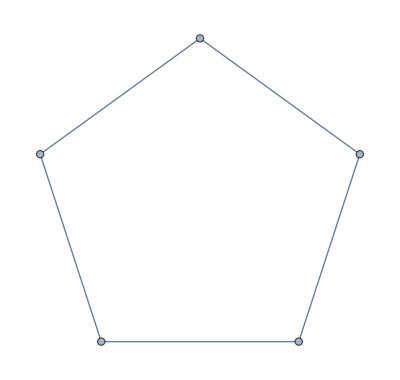

```mathematica
(* Graph - Creates a graph from vertex and edge specifications *)
Graph[{1 -> 2, 2 -> 3, 3 -> 1}]
Graph[Range[5], {1 <-> 2, 2 <-> 3, 3 <-> 4, 4 <-> 5, 5 <-> 1}]
```

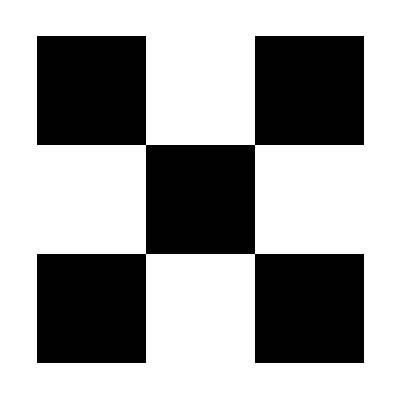

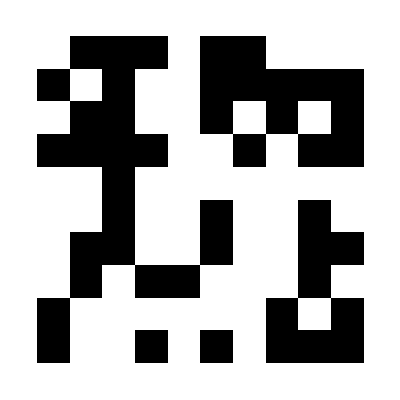

```mathematica
(* ArrayPlot - Visualizes matrices as images *)
ArrayPlot[{{1, 0, 1}, {0, 1, 0}, {1, 0, 1}}]
ArrayPlot[RandomInteger[{0, 1}, {10, 10}]]
```

```mathematica
(* Array - Generates an array of values based on an expression *)
Array[f, 5] (* {f[1], f[2], f[3], f[4], f[5]} *)
Array[Prime, 10] (* First 10 prime numbers *)
```

{f[1],f[2],f[3],f[4],f[5]}

{2,3,5,7,11,13,17,19,23,29}

```mathematica
(* Nest - Applies a function repeatedly *)
Nest[Sqrt, 256, 3] (* sqrt(sqrt(sqrt(256))) *)
Nest[RotateRight, {a, b, c, d}, 2]
```

2

{c,d,a,b}

```mathematica
(* NestList - Like Nest, but returns intermediate results *)
NestList[Sqrt, 256, 3]
NestList[RotateRight, {a, b, c, d}, 2]
```

{256,16,4,2}

{{a,b,c,d},{d,a,b,c},{c,d,a,b}}

```mathematica
(* PrimeQ - Tests if a number is prime *)
PrimeQ[7] (* True *)
PrimeQ[10] (* False *)
```

True

False

```mathematica
(* MemberQ - Checks if an element is in a list *)
MemberQ[{a, b, c}, b] (* True *)
```

True

```mathematica
(* EvenQ - Tests if a number is even *)
EvenQ[4] (* True *)
EvenQ[3] (* False *)
```

True

False

```mathematica
(* Last & First - Get the last/first element of a list *)
Last[{1, 2, 3, 4}]
First[{1, 2, 3, 4}]
```

4

1

```mathematica
(* Select - Filters elements based on a condition *)
Select[Range[10], PrimeQ]
```

{2,3,5,7}

```mathematica
(* Total - Computes the sum of elements *)
Total[{1, 2, 3, 4}]
Total[{{1, 2}, {3, 4}}, {2}] (* Sum along second level *)
```

10

{3,7}

```mathematica
(* Thread - Applies a function element-wise to lists *)
Thread[{a, b, c} + {1, 2, 3}]
Thread[Equal[{a, b, c}, {1, 2, 3}]]
```

{1+a,2+b,3+c}

{a==1,b==2,c==3}

```mathematica
(* Grid - Displays elements in a tabular format *)
Grid[{{"A", "B"}, {1, 2}, {3, 4}}]
```

A | B
1 | 2
3 | 4

```mathematica
(* Partition - Splits a list into sublists *)
Partition[Range[10], 2]
Partition[Range[10], 3, 1] (* Overlapping partitions *)
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

{{1,2,3},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{6,7,8},{7,8,9},{8,9,10}}

```mathematica
(* ArrayFlatten - Flattens nested arrays into a single matrix *)
ArrayFlatten[{{{1, 2}, {3, 4}}, {{5, 6}, {7, 8}}}]
```

{{{1,2},{3,4}},{{5,6},{7,8}}}

```mathematica
(* Flatten - Flattens nested lists *)
Flatten[{{1, {2, 3}}, {4, 5}}]
Flatten[{{1, {2, 3}}, {4, 5}}, 1] (* Flatten only one level *)
```

{1,2,3,4,5}

{1,{2,3},4,5}

```mathematica
(* Max - Finds the maximum element *)
Max[3, 10, 7]
Max[{3, 10, 7}]
```

10

10

```mathematica
(* Split - Groups consecutive identical elements *)
Split[{1, 1, 2, 2, 2, 3, 3, 1}]
```

{{1,1},{2,2,2},{3,3},{1}}

```mathematica
(* GatherBy - Groups elements based on a function *)
GatherBy[{1, 2, 3, 4, 5, 6}, EvenQ]
```

{{1,3,5},{2,4,6}}

```mathematica
(* RandomSample - Randomly selects elements from a list *)
RandomSample[Range[10], 5]
```

{6,7,1,5,2}

```mathematica
(* Tuples - Generates all possible tuples of given length *)
Tuples[{0, 1}, 3] (* All binary strings of length 3 *)
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

```mathematica
(* TakeSmallest - Extracts the smallest elements *)
TakeSmallest[{5, 1, 3, 9, 2}, 3]
```

{1,2,3}

```mathematica
(* Join - Concatenates lists *)
Join[{1, 2}, {3, 4}]
```

{1,2,3,4}

```mathematica
(* ReplacePart - Replaces specified parts of an expression *)
ReplacePart[{a, b, c}, {2 -> x}]
ReplacePart[{{a, b}, {c, d}}, {{1, 2} -> x, {2, 1} -> y}]
```

{a,x,c}

{{a,x},{y,d}}

```mathematica
(* Nothing - Removes elements in a list transformation *)
DeleteCases[{a, Nothing, b}, Nothing]
```

{a,b}

```mathematica
(* /@ and & in Array *)
Sin /@ Range[5] (* Apply Sin to each element *)
Array[#^2 &, 5] (* Square each index *)
```

{Sin[1],Sin[2],Sin[3],Sin[4],Sin[5]}

{1,4,9,16,25}

```mathematica
(* [] vs. // *)
f[x] (* Direct function application *)
x // f (* Same as f[x] *)
```

f[x]

f[x]

```mathematica
(* Cases - Extracts elements matching a pattern *)
Cases[{1, 2, 3, 4, 5}, _Integer?EvenQ]
Cases[IntegerDigits[2^1000], 0 | 1]
Cases[{{a, b, c}, {d, e, f}}, {x_, y_, z_} :> {y, x, z}]
```

{2,4}

{1,0,1,0,0,1,0,0,0,0,0,0,1,1,0,1,0,1,1,0,0,0,0,1,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,1,0,0,0,1,1,1,1,1,0,1,1,1,0,0,1,1,1,1,0,1,0,0}

{{b,a,c},{e,d,f}}

```mathematica
(* Head - Gets the type of an expression *)
Head[3] (* Integer *)
Head[{1, 2, 3}] (* List *)
```

Integer

List

```mathematica
(* IntegerQ - Checks if a number is an integer *)
IntegerQ[5.0] (* False *)
IntegerQ[5] (* True *)
```

False

True

```mathematica
(* Rule - Creates transformation rules *)
{a, b, c} /. a -> x
```

{x,b,c}

```mathematica
(* Keys - Extracts keys from an association *)
Keys[<|"a" -> 1, "b" -> 2|>]
```

{a,b}

## Precedence

Function Application (@): This is used for prefix function application, where f @ x is equivalent to f[x]
Apply (@@): This operator replaces the head of an expression. For example, f @@ {a, b, c} changes the head of {a, b, c} from List to f, resulting in f[a, b, c]
Map (/@): This applies a function to each element in a list. For instance, f /@ {a, b, c} yields {f[a], f[b], f[c]}​


The precedence of these operators:
@ ​
@@ ​
/ (Various operators like division)
/; (Condition)
/= (UpSet)​
/. (ReplaceAll)
// (Postfix)
/@ ​

To determine the precedence of operators: Precedence.
Precedence[Apply]    (* Output: 650 *)
Precedence[ReplaceAll]      (* Output: 110 *)
Higher values indicate higher precedence.

```mathematica
Precedence[Apply]    (*Output:650*)
Precedence[ReplaceAll]      (*Output:110*)
```

620.

110.